Two-Focus FCS

Literature:paclet:Fretica/tutorial/Two-FocusFCS#395868266 | F2fFCSFitpaclet:Fretica/tutorial/Two-FocusFCS#500366741
Fitting modelpaclet:Fretica/tutorial/Two-FocusFCS#301969416 |

```mathematica
Needs["Fretica`"]
```

Literature:

Dertinger, Thomas, et al. "Two-focus fluorescence correlation spectroscopy: A new tool for accurate and absolute diffusion measurements." ChemPhysChem 8.3 (2007): 433-443.https://doi.org/10.1002/cphc.200600638
Arbour, Tyler J., and Jörg Enderlein. "Application of dual-focus fluorescence correlation spectroscopy to microfluidic flow-velocity measurement." Lab on a Chip 10.10 (2010): 1286-1292.https://doi.org/10.1039/B924594D

Fitting model

F2fFCSFit

```mathematica
?F2fFCSFromTTTR
?F2fFCSGetModel
?F2fFCSFit
?F2fFCSGetLinearCoefficients
?F2fFCSGlobalFit
```

```mathematica
F2fFCSSettings[{0.485,0.515,0.440,150,60}]
```

{F2fFCSLambdaex→0.485,F2fFCSLambdaem→0.515,F2fFCSfocidistance→0.44,F2fFCSpinhole→150,F2fFCSmagnification→60}

Units are  micrometer and milliseconds!

```mathematica
FOpenTTTR[$FreticaExamples<>"\\DualfocusFCS in mixer.ht3"]
```

1

```mathematica
FPIEChannelSelector[{2,4}]
```

```mathematica
chrangefocus1=FGetChannelConstraints[][[1]]
chrangefocus2=FGetPIEChannelConstraints[][[1]]
```

{1,32767}

{1,32767}

```mathematica
chrangefocus1={49,1594};
chrangefocus2={1655,3127};
```

```mathematica
detector1={0,1,0,0};
detector2={0,0,0,1};
fcsdat=F2fFCSFromTTTR[-7,0.,0.03,detector1,detector2,chrangefocus1,chrangefocus2];
```

A fit with one diffusive species, one triplet time and flow in x direction:

```mathematica
nrefractive=1.33;
fitresult=F2fFCSFit[fcsdat,{diff},{vx,0,0},{1/τT},w0,R0,nrefractive,{{diff,0.4},{vx,1.},{τT,.001},{w0,.300},{R0,.150}}]
fitresult[[-1]]
```

-Graphics-

-Graphics-

Results are in units of μm^2/ms,μm/ms,ms, μm ,and  μm, respectively.

```mathematica
F2fFCSGetModel[fcsdat,{diff},{vx,0,0},{1/τT},w0,R0,1.33]/.fitresult[[2]]
```

-Graphics-

```mathematica
modeldatdat=F2fFCSGetModel[fcsdat,{diff},{vx,0,0},{1/τT},w0,R0,1.33,FOutput->FData]/.fitresult[[2]];
ListPlot[modeldatdat]
```

-Graphics-

Change amplitudes manually:

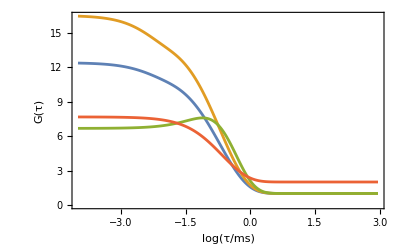

```mathematica
logtimes=fcsdat[[1,All,1]];
aD ={1,1.3} ;(*amplitudes of diffusion term of the autocorrelations*)
aT={1,2,0,0}; (*amplitudes of triplet terms for all four curves*)
offsets={1,1,1,2}; (*offsets for all four curves*)
F2fFCSGetModel[logtimes,{{diff,aD}},{vx,0,0},{{1/τT,aT}},offsets,w0,R0,1.33,FOutput->FGraph]/.fitresult[[2]]
```

### F2fFCSGetLinearCoefficients

```mathematica
{g11,g22,g12,g21}=F2fFCSGetLinearCoefficients[fcsdat,{diff},{vx,0,0},{1/τT},w0,R0,1.33]/.fitresult[[2]];
```

```mathematica
{components,coeff}=g11;
coeff
components[[1;;5]]
```

{0.0358391,0.0247598,1.00132}

{{10.3915,0.974391,1.},{10.3881,0.961833,1.},{10.3848,0.949438,1.},{10.3814,0.937202,1.},{10.378,0.925124,1.}}

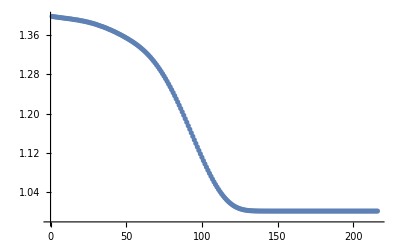

```mathematica
ListPlot[coeff.componentsᵀ]
```

| Related Guides
▪Fretica